## Constructing the Matrix Corresponding to the Derivative Operator, on the Full Basis and Sparse Basis 2D [need to check spectrum]

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=ϕ[2^l(#-2^-l(2i-1))]&
ϕ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx(2i-1))]ϕ[2^ly(#2-2^-ly(2j-1))]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_]:=1+Floor[x]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)
```

### Test Functions, if you like

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
dytest2D[x_,y_]:=2Pi Sin[Pi x]^2 Sin[Pi y] Cos[Pi y]
```

### Standard Basis

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]

standardCoefficients2D[f_,lx_,ly_]:=Table[f[2^-lx i,2^-ly j],{i,1,2^lx-1},{j,1,2^ly-1}]
standardReconstruct2D[coefficients_,lx_,ly_]:=Sum[coefficients[[i,j]] ψ[lx,ly,i,j][#1,#2],{i,1,2^lx-1},{j,1,2^ly-1}]&

standardProject2D[f_,lx_,ly_]:=standardReconstruct2D[standardCoefficients2D[f,lx,ly],lx,ly]
```

```mathematica
Plot3D[#[x,y],{x,0,1},{y,0,1}]&[standardProject2D[test2D,4,4]]
```

-Graphics3D-

### Full Basis

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]

fullCoefficients2DFlat[f_,lx_,ly_]:=Module[{kx,ky,i,j,ans},ans={};For[kx=1,kx≤lx ,kx++,For[ky=1,ky≤ly,ky++,For[i=1,i≤ 2^kx-1,i+=2,For[j=1,j≤ 2^ky-1,j+=2,AppendTo[ans,getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky]]]]]];Return[ans];]

Reconstruct2D[coefficients_]:= If[#1==1||#2==1,0,Sum[coefficients[[lx,ly,ceil[2^(lx-1)#1],ceil[2^(ly-1)#2]]] ϕ[2^lx(#1-2^-lx(2ceil[2^(lx-1)#1]-1))] ϕ[2^ly(#2-2^-ly(2ceil[2^(ly-1)#2]-1))],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]]&

Reconstruct2DFlat[coefficients_,kx_,ky_]:=Reconstruct2D[reverseFlatten[coefficients,kx,ky]]

(*Module[{k},k=0;Return[If[#1==1||#2==1,0,Sum[Sum[coefficients[[++k]] ϕ[2^lx(#1-2^-lx(2i-1))] ϕ[2^ly(#2-2^-ly(2j-1))],{i,1,2^(lx-1)},{j,1,2^(ly-1)}],{lx,1,kx},{ly,1,ky}]]&];]
*)
reverseFlatten[coefficients_,kx_,ky_]:=Module[{k},k=0;Return[Table[Table[coefficients[[++k]] ,{i,1,2^(lx-1)},{j,1,2^(ly-1)}],{lx,1,kx},{ly,1,ky}]];]

(*Module[{i,kx,ky,ans},ans=(0 #1#2)&;i=1; For[kx=1,kx≤lx,kx++,For[ky=1,ky≤ly,ky++,ans=(ans[#1,#2]+coefficients[[i]] ϕ[2^kx(#1-2^-kx(2ceil[2^(kx-1)#1]-1))] ϕ[2^ky(#2-2^-ky(2ceil[2^(ky-1)#2]-1))]&);i++;]]; Return[ans];]
*)
project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f//N,lx,ly]]
```

```mathematica
N[fullCoefficients2D[test2D,3,3]]
reverseFlatten[fullCoefficients2D[test2D,3,3]//Flatten,3,3]//N

Plot3D[#[x,y],{x,0,1},{y,0,1}]&@Reconstruct2DFlat[N[fullCoefficients2DFlat[test2D//N,3,3]],3,3]
Plot3D[#[x,y],{x,0,1},{y,0,1}]&@Reconstruct2D[N[fullCoefficients2D[test2D//N,3,3]]]
```

{{{{1.}},{{0.,0.}},{{-0.103553,0.103553,0.103553,-0.103553}}},{{{0.},{0.}},{{0.,0.},{0.,0.}},{{0.,0.,0.,0.},{0.,0.,0.,0.}}},{{{-0.103553},{0.103553},{0.103553},{-0.103553}},{{0.,0.},{0.,0.},{0.,0.},{0.,0.}},{{0.0107233,-0.0107233,-0.0107233,0.0107233},{-0.0107233,0.0107233,0.0107233,-0.0107233},{-0.0107233,0.0107233,0.0107233,-0.0107233},{0.0107233,-0.0107233,-0.0107233,0.0107233}}}}

{{{{1.}},{{0.,0.}},{{-0.103553,0.103553,0.103553,-0.103553}}},{{{0.},{0.}},{{0.,0.},{0.,0.}},{{0.,0.,0.,0.},{0.,0.,0.,0.}}},{{{-0.103553},{0.103553},{0.103553},{-0.103553}},{{0.,0.},{0.,0.},{0.,0.},{0.,0.}},{{0.0107233,-0.0107233,-0.0107233,0.0107233},{-0.0107233,0.0107233,0.0107233,-0.0107233},{-0.0107233,0.0107233,0.0107233,-0.0107233},{0.0107233,-0.0107233,-0.0107233,0.0107233}}}}

-Graphics3D-

-Graphics3D-

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,2^-row i,2^(-(diag-row+1)) j,row,(diag-row+1)],{i,1,2^row-1,2},{j,1,2^(diag-row+1)-1,2}],{row,1,diag}],{diag,1,n}]

sparseReconstruct[coefficients_]:=If[#1==1||#2==1,0,Sum[Sum[coefficients[[diag,row,ceil[2^(row-1)#1],ceil[2^(diag-row)#2]]] ϕ[2^row(#1-2^-row(2ceil[2^(row-1)#1]-1))] ϕ[2^(diag-row+1)(#2-2^(-(diag-row+1))(2ceil[2^(diag-row)#2]-1))],{row,1,Length[coefficients[[diag]]]}],{diag,1,Length[coefficients]}]]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]
```

### Differentiation

```mathematica
diffx[f_,l_]:=If[#1< 2^-l, diffx[diffx[f,l+1],l+1][2^-l,#2]#1,If[#1> 1-2^-l, diffx[diffx[f,l+1],l+1][1-2^-l,#2](#1-1),(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&

diffy[f_,l_]:=If[#2< 2^-l, diffy[diffy[f,l+1],l+1][#1,2^-l]#2,If[#2> 1-2^-l, diffy[diffy[f,l+1],l+1][#1,1-2^-l](#2-1),(f[#1,#2+2^-l]-f[#1,#2-2^-l])/(2 2^-l)]]&
```

### Algorithms to form the Matrices

```mathematica
dxMatrix[lx_,ly_]:=Table[Table[fullCoefficients2D[diffx[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(kx-1)},{j,1,2^(ky-1)}],{kx,1,lx},{ky,1,ly}]
dyMatrix[lx_,ly_]:=Table[Table[fullCoefficients2D[diffy[ϕ[kx,ky,i,j],ly],lx,ly]//Flatten,{i,1,2^(kx-1)},{j,1,2^(ky-1)}],{kx,1,lx},{ky,1,ly}]


dxMatrixStandard[lx_,ly_]:=Table[standardCoefficients2D[diffx[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,1,2^lx-1},{j,1,2^ly-1}]
dyMatrixStandard[lx_,ly_]:=Table[standardCoefficients2D[diffy[ψ[lx,ly,i,j],ly],lx,ly]//Flatten,{i,1,2^lx-1},{j,1,2^ly-1}]


dxMatrixSparse[n_]:=Table[Table[Table[sparseCoefficients2D[diffx[ϕ[row,diag-row+1,i,j],n],n]//Flatten,{i,1,2^(row-1)},{j,1,2^(diag-row)}],{row,1,diag}],{diag,1,n}]

dyMatrixSparse[n_]:=Table[Table[Table[sparseCoefficients2D[diffy[ϕ[row,diag-row+1,i,j],n],n]//Flatten,{i,1,2^row-1,2},{j,1,2^(diag-row+1)-1,2}],{row,1,diag}],{diag,1,n}]
```

-Graphics3D-

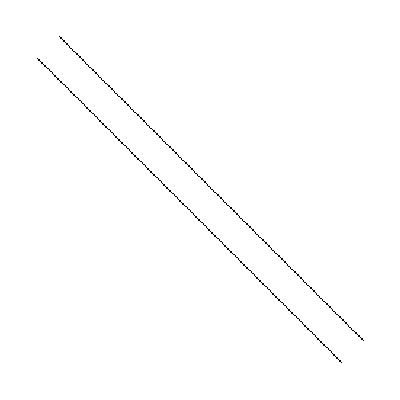

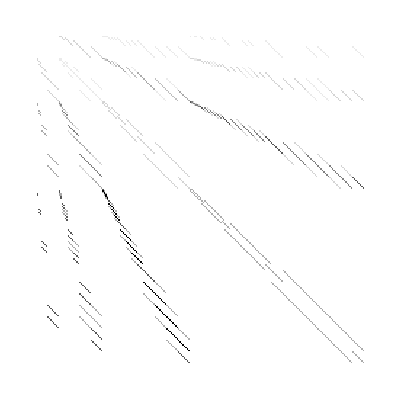

```mathematica
Plot3D[#[x,y],{x,0,1},{y,0,1},PlotRange->Full]&@Reconstruct2DFlat[Flatten[N[dxMatrix[3,3]],3][[1]],3,3]
Flatten[N[dxMatrixStandard[4,4]],1]//ArrayPlot
Flatten[N[dxMatrix[4,4]],3]//ArrayPlot
```

```mathematica
{fullCoefficients2D[diffx[ϕ[1,1,1,1],3],3,3]//Flatten,fullCoefficients2D[diffx[ϕ[1,2,1,1],3],3,3]//Flatten,fullCoefficients2D[diffx[ϕ[1,2,1,2],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[1,2,1,3],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,1,1,1],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,1,2,1],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,1,3,1],3],3,3]//Flatten,fullCoefficients2D[diffx[ϕ[2,2,1,1],3],3,3]//Flatten,fullCoefficients2D[diffx[ϕ[2,2,1,2],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,1,3],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,2,1],3],3,3]//Flatten,fullCoefficients2D[diffx[ϕ[2,2,2,2],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,2,3],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,3,1],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,3,2],3],3,3]//Flatten,
fullCoefficients2D[diffx[ϕ[2,2,3,3],3],3,3]//Flatten}//ArrayPlot
```

-Graphics-

```mathematica
Flatten[N[dxMatrixSparse[3]],3]//Eigenvalues
```

{-3.83169×10^-17+7.39104 ⅈ,-3.83169×10^-17-7.39104 ⅈ,5.55112×10^-16+5.65685 ⅈ,5.55112×10^-16-5.65685 ⅈ,3.47136×10^-17+3.06147 ⅈ,3.47136×10^-17-3.06147 ⅈ,2.08167×10^-16+2.82843 ⅈ,2.08167×10^-16-2.82843 ⅈ,-5.55112×10^-17+2.82843 ⅈ,-5.55112×10^-17-2.82843 ⅈ,1.91087×10^-16+0. ⅈ,9.59198×10^-17+0. ⅈ,-1.18532×10^-17+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

### Example

#### Standard Case:

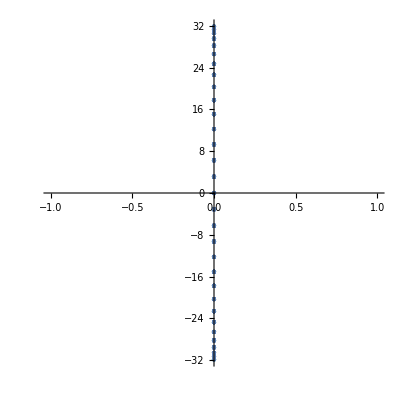

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[N[dxMatrixStandard[5,5]],1]//Eigenvalues,3],AspectRatio->1]
```

#### Full Hierarchical Case:

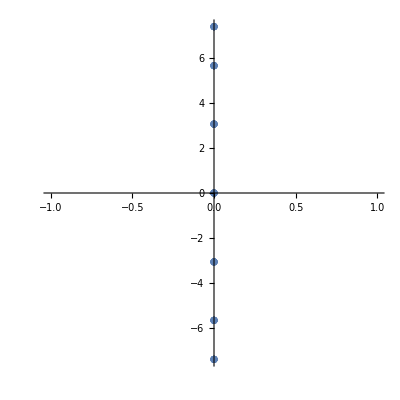

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[N[dxMatrix[3,3]],3]//Eigenvalues,3],AspectRatio->1]
```

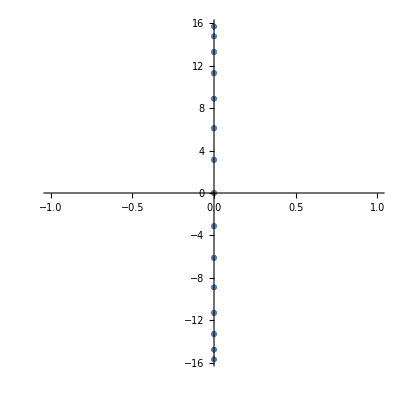

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[N[dxMatrix[4,4]],3]//Eigenvalues,3],AspectRatio->1]
```

#### Sparse Case:

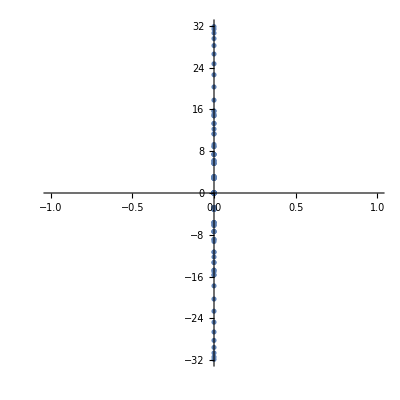

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[N[dxMatrixSparse[5]],3]//Eigenvalues,3],AspectRatio->1]
```